```mathematica
B= {{1-(a^2/(sigmaX^2*sigmaY^2)),(-a*b)/(sigmaX^2*sigmaY^2)},{(-a*b)/(sigmaX^2*sigmaY^2),1-(b^2/(sigmaX^2*sigmaY^2))}}
```

{{1-a^2/(sigmaX^2 sigmaY^2),-(a b)/(sigmaX^2 sigmaY^2)},{-(a b)/(sigmaX^2 sigmaY^2),1-b^2/(sigmaX^2 sigmaY^2)}}

```mathematica
{vals,vecs}=Eigensystem[B]
```

{{1,(-a^2-b^2+sigmaX^2 sigmaY^2)/(sigmaX^2 sigmaY^2)},{{-b/a,1},{a/b,1}}}

```mathematica
index = 2
```

2

```mathematica
alpha=Sqrt[((beta*(1-vals[[index]]))-1)/(vals[[index]]*Inner[Times,vecs[[index]],vecs[[index]],Plus]*sigmaX^2)]
```

√((sigmaY^2 (-1+beta (1-(-a^2-b^2+sigmaX^2 sigmaY^2)/(sigmaX^2 sigmaY^2))))/((1+a^2/b^2) (-a^2-b^2+sigmaX^2 sigmaY^2)))

```mathematica
vecs[[index]]
```

{a/b,1}

```mathematica
g[a_,b_,sigmaX_,sigmaY_]:=alpha*vecs[[index]]
```

```mathematica
g[a,c,sigmaX,sigmaY]
```

{(a √((sigmaY^2 (-1+beta (1-(-a^2-b^2+sigmaX^2 sigmaY^2)/(sigmaX^2 sigmaY^2))))/((1+a^2/b^2) (-a^2-b^2+sigmaX^2 sigmaY^2))))/b,√((sigmaY^2 (-1+beta (1-(-a^2-b^2+sigmaX^2 sigmaY^2)/(sigmaX^2 sigmaY^2))))/((1+a^2/b^2) (-a^2-b^2+sigmaX^2 sigmaY^2)))}

```mathematica
Clear[derivA]
derivA[a_,b_,beta_,sigmaX_,sigmaY_]=FullSimplify[D[g[a,b,sigmaX,sigmaY],a]]
```

{(-b^3 (a^2+b^2)^2 beta+b (a^2+b^2) (a^2 (-1+beta)+b^2 (1+beta)) sigmaX^2 sigmaY^2-b^3 sigmaX^4 sigmaY^4)/((a^2+b^2)^2 sigmaX^2 (a^2+b^2-sigmaX^2 sigmaY^2)^2 √((b^2 (-(a^2+b^2) beta+sigmaX^2 sigmaY^2))/((a^2+b^2) sigmaX^2 (a^2+b^2-sigmaX^2 sigmaY^2)))),(a b^2 ((a^2+b^2)^2 beta-2 (a^2+b^2) sigmaX^2 sigmaY^2+sigmaX^4 sigmaY^4))/((a^2+b^2)^2 sigmaX^2 (a^2+b^2-sigmaX^2 sigmaY^2)^2 √((b^2 (-(a^2+b^2) beta+sigmaX^2 sigmaY^2))/((a^2+b^2) sigmaX^2 (a^2+b^2-sigmaX^2 sigmaY^2))))}

```mathematica
derivA[0.1,0.2,100,1,1][[1]]
derivA[a,b,beta,sigmaX,sigmaY][[2]]
```

9.73206

(a b^2 ((a^2+b^2)^2 beta-2 (a^2+b^2) sigmaX^2 sigmaY^2+sigmaX^4 sigmaY^4))/((a^2+b^2)^2 sigmaX^2 (a^2+b^2-sigmaX^2 sigmaY^2)^2 √((b^2 (-(a^2+b^2) beta+sigmaX^2 sigmaY^2))/((a^2+b^2) sigmaX^2 (a^2+b^2-sigmaX^2 sigmaY^2))))

```mathematica
derivA[a,b,beta,1,1][[2]]
```

(a b^2 (1-2 (a^2+b^2)+(a^2+b^2)^2 beta))/((-1+a^2+b^2)^2 (a^2+b^2)^2 √((b^2 (1-(a^2+b^2) beta))/((-1+a^2+b^2) (a^2+b^2))))

```mathematica
plot3dA1=Plot3D[derivA[a,b,100,1,1][[1]],{a,-0.8,0.8},{b,-0.8,0.8},AxesLabel->{a,b}];
```

```mathematica
plotanimateA1=Animate[Plot[derivA[a,c*a,100,1,1][[1]],{a,0.1,0.9}],{c,0.1,0.9},AnimationRunning->False];
```

```mathematica
plotcontourA1=ContourPlot[derivA[a,b,100,1,1][[1]],{a,0.1,0.9},{b,0.1,0.9},AxesLabel->Automatic];
```

```mathematica
plot3dA2=Plot3D[derivA[a,b,100,1,1][[2]],{a,0.1,0.9},{b,0.1,0.9},PlotStyle->Directive[Yellow,Specularity[White,20],Opacity[0.8]],AxesLabel->{a,b}];
```

```mathematica
plotcontourA2=ContourPlot[derivA[a,b,100,1,1][[2]],{a,0.1,0.9},{b,0.1,0.9},AxesLabel->Automatic];
```

```mathematica
Clear[derivB]
derivB[a_,b_,beta_,sigmaX_,sigmaY_]=FullSimplify[D[g[a,b,sigmaX,sigmaY],b]];
```

```mathematica
derivB[a,b,beta,sigmaX,sigmaY][[1]]
```

(a b^2 ((a^2+b^2)^2 beta-2 (a^2+b^2) sigmaX^2 sigmaY^2+sigmaX^4 sigmaY^4))/((a^2+b^2)^2 sigmaX^2 (a^2+b^2-sigmaX^2 sigmaY^2)^2 √((b^2 (-(a^2+b^2) beta+sigmaX^2 sigmaY^2))/((a^2+b^2) sigmaX^2 (a^2+b^2-sigmaX^2 sigmaY^2))))

```mathematica
FullSimplify[derivB[rx1y*sigmaX*sigmaY,rx2y*sigmaX*sigmaY,beta,sigmaX,sigmaY][[1]]]
```

(rx1y rx2y^2 (1+beta rx1y^4-2 rx2y^2+beta rx2y^4+2 rx1y^2 (-1+beta rx2y^2)))/((-1+rx1y^2+rx2y^2)^2 (rx1y^2+rx2y^2)^2 √(-(rx2y^2 (-1+beta (rx1y^2+rx2y^2)))/((-1+rx1y^2+rx2y^2) (rx1y^2+rx2y^2) sigmaX^2)) sigmaX^3 sigmaY)

```mathematica
derivA[a,b,beta,sigmaX,sigmaY][[2]]
```

(a b^2 ((a^2+b^2)^2 beta-2 (a^2+b^2) sigmaX^2 sigmaY^2+sigmaX^4 sigmaY^4))/((a^2+b^2)^2 sigmaX^2 (a^2+b^2-sigmaX^2 sigmaY^2)^2 √((b^2 (-(a^2+b^2) beta+sigmaX^2 sigmaY^2))/((a^2+b^2) sigmaX^2 (a^2+b^2-sigmaX^2 sigmaY^2))))

```mathematica
plot3dB1=Plot3D[derivB[a,b,100,1,1][[1]],{a,0.1,0.9},{b,0.1,0.9}];
```

```mathematica
plotcontourB1=ContourPlot[derivB[a,b,100,1,1][[1]],{a,0.1,0.9},{b,0.1,0.9},AxesLabel->Automatic];
```

```mathematica
plot3dB2=Plot3D[derivB[a,b,100,1,1][[2]],{a,0.1,0.9},{b,0.1,0.9},AxesLabel->Automatic];
```

```mathematica
plotcontourB2=ContourPlot[derivB[a,b,100,1,1][[2]],{a,0.1,0.9},{b,0.1,0.9},AxesLabel->Automatic,BaseStyle->Directive[Opacity[0.5]]];
```

```mathematica
derivB[0.1,0.2,100,1,1];
```

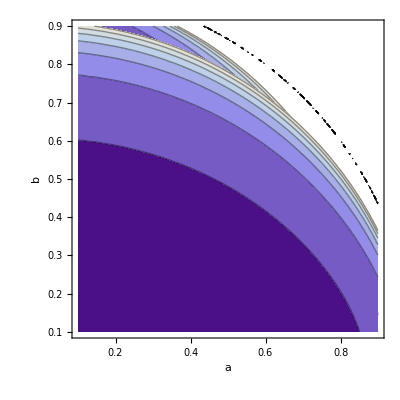

```mathematica
Show[plotcontourA1,plotcontourB2]
```